```mathematica
f[x_] = 1/(1 + x)
```

1/(1+x)

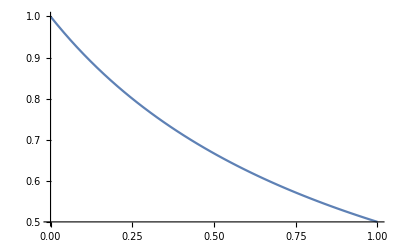

```mathematica
Plot[f[x], {x, 0 , 1}]
```

```mathematica
l0[x_] = (x -1)/-1
```

1-x

```mathematica
l1[x_] = x/1
```

x

```mathematica
p[x_] = 1 * l0[x] + 1/2* l1[x]
```

1-x/2

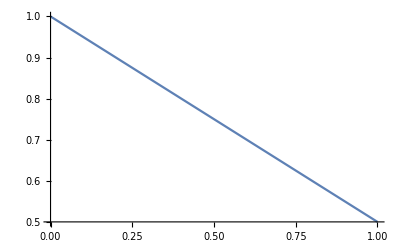

```mathematica
Plot[p[x], {x, 0, 1}]
```

```mathematica
err[x_] = f[x] - p[x]
```

-1+x/2+1/(1+x)

```mathematica
maxErr[x_] = x * (x -1)
```

(-1+x) x

```mathematica
Plot[Abs[maxErr]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

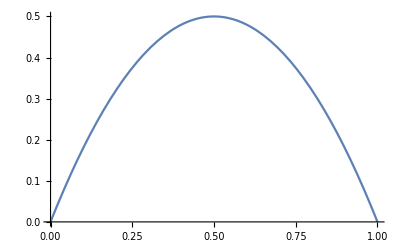

```mathematica
Plot[Abs[2*maxErr[x]], {x, 0, 1}]
```

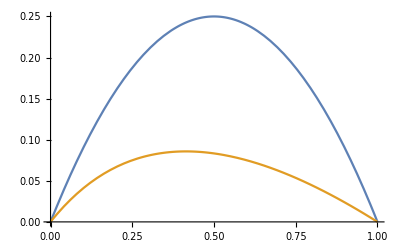

```mathematica
Plot[{Abs[maxErr[x]], Abs[err[x]]}, {x, 0,1 }]
```